## Aufgabe 1

```mathematica
Integrate[x*Sin[x],x]
```

-x Cos[x]+Sin[x]

```mathematica
Integrate[x*Sin[x^2],x]
```

-1/2 Cos[x^2]

```mathematica
Integrate[x/(1+x^2),x]
```

1/2 Log[1+x^2]

```mathematica
Integrate[(1+x)/(1-x),x]
```

-x-2 Log[1-x]

```mathematica
Integrate[s*E^s^2,s]
```

(ⅇ^(s^2))/2

```mathematica
Integrate[t^2*E^t,t]
```

ⅇ^t (2-2 t+t^2)

## Aufgabe 3

```mathematica
f[x_]:=x^3+x^2-2x
```

### Ableitungen

```mathematica
f'[x]
f''[x]
f'''[x]
f''''[x]
```

-2+2 x+3 x^2

2+6 x

6

0

### Nullstellen

```mathematica
Solve[f[x]==0,x]
```

{{x→-2},{x→0},{x→1}}

Nullstellen bei x1=-2, x2 = 0, x3=1

Extremwerte

```mathematica
Solve[f'[x]==0,x]
```

{{x→1/3 (-1-√7)},{x→1/3 (-1+√7)}}

```mathematica
N[%]
```

{{x→-1.21525},{x→0.548584}}

```mathematica
f''[1/3 (-1-√7)]
```

2+2 (-1-√7)

```mathematica
%<0
```

True

```mathematica
FullSimplify[f[1/3 (-1-√7)]]
```

2/27 (10+7 √7)

```mathematica
N[%]
```

2.11261

Maximum bei (1/3 (-1-√7),2/27 (10+7 √7))

```mathematica
f''[1/3 (-1+√7)]
```

2+2 (-1+√7)

```mathematica
% >0
```

True

```mathematica
FullSimplify[f[1/3 (-1+√7)]]
```

-2/27 (-10+7 √7)

```mathematica
N[%]
```

-0.63113

Minimum bei ((1/3 (-1-√7),2/27 (10+7 √7))

Wendepunkte

```mathematica
Solve[f''[x]==0,x]
```

{{x→-1/3}}

```mathematica
f'''[-1/3]
```

6

```mathematica
f[-1/3]
```

20/27

Wendepunkt bei (-1/3, 20/27)

```mathematica
f'[-1/3]
```

-7/3

```mathematica
FullSimplify[Solve[-7/3*(-1/3)+d==20/27,d]]
```

{{d→-1/27}}

Wendetangente y = -7/3 x -1/27

Graph

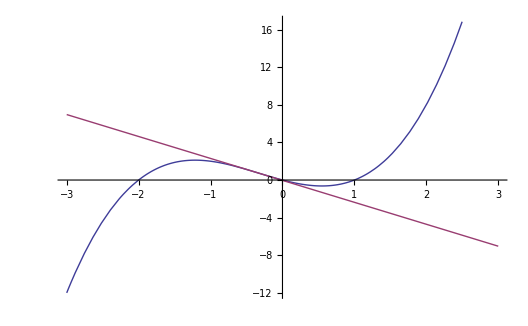

```mathematica
Plot[{f[x],-7/3 x-1/27},{x,-3,3}]
```